```mathematica
α=7.297352533 10^-3;
H[x_,y_,β_]:=(α*β)/(2*π)*(1/(√(x*(1-x)))*ArcTan[√(x/(1-x))]-1+π(λ[y,β] x)/(1-x-λ[y,β]^2)) Exp[-(2y)/β];
H0[x_,y_,β_]:= α*β*(1/(4 √(1-x))+1/2 λ[y,β]/(1-x-λ[y,β]^2)) Exp[-(2y)/β];
dH[x_,y_,β_]:=((x+(2 *x -1))/(2*x^2*(1-x)) √(x/(1-x))ArcTan[ √(x/(1-x))]+(π(1-λ[y,β])^2 λ[y,β])/((1-λ[y,β]^2-x)^2))Exp[-(2y)/β];
u1[y_,β_]:=(2 β^2)/(α^2 y^2)*Exp[ExpIntegralEi[-(2y)/β]];
λ[y_,β_]:= α/2 (Log[4.5 u1[y,β]]-2.44 Log[Log[0.15 u1[y,β]]]);
```

```mathematica
LDis2=Table[x/.FindRoot[x-y+H[x,y,50],{x,0.1,0.9999},MaxIterations->1000],{y,0.0000000001,4,0.1}];
LDis22={9.434635967561247*^-11,0.09513761239091803,0.1895218961229348,0.2828665037624005,0.3748122205931552,0.46483964712193426,0.552171889763471,0.6356268124898627,0.7134197883656693,0.7830219622497376,0.8414548738850327,0.8865493224128879,0.9185669948156328,0.9401371672221822,0.9545058246938914,0.964246858774896,0.9710523779418277,0.9759641076538447,0.9796188350235085,0.9824129541232576,0.9846000763829003,0.9863473156348466,0.9877679727818305,0.9889409172202861,0.9899223805064212,0.9907533274030675,0.9914641838597664,0.9920779444872123,0.9926122615890388,0.9930808789940543,0.9934946350903593,0.9938621768765737,0.9941904763701203,0.9944852097712769,0.9947510394823479,0.9949918265869404,0.9952107927595936,0.9954106449652232};
LDis3=Table[x/.FindRoot[x-y+H[x,y,50],{x,0.99,0.9991},MaxIterations->1000],{y,4,20,0.1}];
LDis32={0.9959167626869344,0.9960599250272218,0.9961925486415812,0.9963157090850464,0.9964303443244513,0.9965372756031392,0.9966372247854881,0.9967308286882505,0.9968186510005451,0.9969011923237173,0.9969788986032333,0.9970521682539352,0.997121358222669,0.9971867891570805,0.9972487498149608,0.9973075008780575,0.9973632782114114,0.9974162957060742,0.9974667477269171,0.9975148112666619,0.9975606477990311,0.9976044049112912,0.9976462177552147,0.9976862102983562,0.9977244964325926,0.9977611809688024,0.9977963605030602,0.9978301241981403,0.9978625544660202,0.9978937275914767,0.9979237142760101,0.9979525801331753,0.99798038613035,0.9980071889859996,0.9980330415273998,0.9980579930133434,0.9980820894245006,0.9981053737296961,0.9981278861219057,0.9981496642366292,0.9981707433485749,0.9981911565508585,0.9982109349195587,0.998230107660085,0.9982487022464249,0.998266744543834,0.9982842589250536,0.9983012683715682,0.9983177945732645,0.9983338580143051,0.9983494780562508,0.9983646730114052,0.9983794602126042,0.998393856076663,0.998407876162708,0.9984215352300649,0.9984348472812677,0.9984478256165693,0.9984728310641052,0.9984848816210287,0.9984966454230257,0.9985081328317698,0.9985193537214686,0.9985303175056968,0.998541033166299,0.9985515092727749,0.9985617540102427,0.9985717751979183,0.9985815803097993,0.9985911764927363,0.9986005705851464,0.9986097691314921,0.9986187783993031,0.9986276043923467,0.998636252866391,0.9986447293375782,0.9986530390989835,0.9986611872299606,0.9986691786051164,0.9986770179067419,0.9986847096342579,0.9986922581100699,0.998699667491213,0.9987069417756177,0.9987140848098554,0.998721100296072,0.99872799179913,0.9987347627517688,0.9987414164622008,0.9987479561179353,0.9987543847925079,0.9987607054498938,0.9987669209494162,0.9987730340502923,0.9987790474159435,0.9987849636179931,0.9987907851405932,0.9987965143832435,0.9988021536651588,0.9988077052281812,0.998813171240033,0.9988185537973354,0.9988238549284807,0.998829076596266,0.9988442835209423,0.9988540574223258,0.9988588401774523,0.9988682051536978,0.9988727903753614,0.998877312678285,0.9988817734529819,0.9988861740489351,0.9988905157760999,0.9988947999063283,0.998899027674741,0.9989032002810397,0.998907318890763,0.9989113846364901,0.998915398618994,0.9989193619083475,0.9989232755449826,0.9989271405407072,0.9989309578796807,0.9989347285193414,0.9989384533913391,0.9989421334023443,0.9989457694349129,0.9989493623482734,0.998952912979091,0.9989564221422025,0.9989598906313225,0.9989633192197007,0.9989667086608749,0.9989700596891312,0.9989733730202377,0.9989766493519888,0.9989798893647654,0.9989830937220752,0.9989862630710726,0.9989893980430594,0.9989924992539677,0.9989955673048256,0.9989986027822048,0.9990016062586531,0.9990045782931125,0.9990075194312837,0.999010430206189,0.9990133111382248,0.9990161627358045,0.9990189854956026,0.9990217799028964,0.9990245464318922,0.9990272855460458,0.9990299976983604,0.9990326833316847,0.9990353428789939};
LDis4=Table[x/.FindRoot[x-y+H[x,y,50],{x,0.1,0.9991},MaxIterations->1000],{y,20,50,0.1}];
LDis42={0.999035342878994,0.9990379767636662,0.9990405853997416,0.9990431691922048,0.9990457285371817,0.9990482638222291,0.9990507754265506,0.9990532637212066,0.9990557290693484,0.999058171826448,0.9990605923404381,0.9990629909519784,0.9990653679946214,0.99906772379496,0.9990700586728951,0.9990723729417231,0.9990746669083456,0.9990769408734284,0.9990791951315562,0.9990814299713885,0.9990836456757833,0.9990858425220638,0.9990880207819164,0.9990901807217677,0.999092322602798,0.9990944466810906,0.999096553207757,0.999098642429071,0.9991007145865498,0.9991027699171124,0.9991048086531619,0.9991068310226975,0.9991088372493927,0.9991108275528887,0.999112802148465,0.9991147612475856,0.9991167050577592,0.9991186337826969,0.9991205476223427,0.9991224467729845,0.9991243314274499,0.999126201774997,0.99912805800151,0.999129900289551,0.9991317288184332,0.999133543764294,0.9991353453001662,0.9991371335960461,0.99913890881896,0.9991406711330306,0.9991424206995401,0.999144157676991,0.9991458822211912,0.9991475944852026,0.9991492946195949,0.9991509827723376,0.9991526590889135,0.9991543237123458,0.9991559767832956,0.9991576184400943,0.9991592488187429,0.9991608680530313,0.9991624762745467,0.9991640736127259,0.9991656601948974,0.9991672361463204,0.9991688015903024,0.9991703566480428,0.9991719014388971,0.9991734360802956,0.9991749606878065,0.9991764753751738,0.9991779802543543,0.9991794754355589,0.999180961027223,0.9991824371362026,0.9991839038676243,0.9991853613250166,0.9991868096103191,0.9991882488239127,0.9991896790646645,0.9991911004299208,0.9991925130155753,0.9991939169160765,0.9991953122244576,0.9991966990323713,0.9991980774300993,0.9991994475065952,0.9992008093495001,0.9992021630451697,0.9992035086786972,0.9992048463339371,0.9992061760935282,0.9992074980389156,0.9992088122503724,0.9992101188070215,0.9992114177868558,0.9992127092667595,0.9992139933225271,0.9992152700288837,0.9992165394595034,0.9992178016870291,0.9992190567830895,0.9992203048183179,0.9992215458623694,0.9992227799839384,0.9992240072507745,0.9992252277297003,0.9992264414866263,0.9992276485865674,0.999228849093658,0.9992300430711669,0.9992312305815129,0.9992324116862786,0.9992335864462247,0.9992347549213043,0.999235917170676,0.9992370732527174,0.9992382232250387,0.9992393671444795,0.9992405050671899,0.9992416370485273,0.9992427631431569,0.9992438834050378,0.9992449978874339,0.9992461066429256,0.9992472097234213,0.9992483071801674,0.999249399063761,0.9992504854241577,0.9992515663106843,0.9992526417720478,0.999253711856345,0.9992547766110647,0.9992558360831347,0.9992568903188656,0.9992579393640113,0.9992589832637631,0.9992600220627569,0.9992610558050837,0.999262084534297,0.9992631082934212,0.9992641271249607,0.9992651410709068,0.9992661501727462,0.9992671544714572,0.9992681540075717,0.9992691488210832,0.9992701389515388,0.9992711244380161,0.9992721053191316,0.9992730816330481,0.9992740534174809,0.999275020709709,0.9992759835465655,0.9992769419644741,0.9992778959994266,0.9992788456869958,0.9992797910623726,0.999280732160307,0.9992816690151769,0.9992826016609625,0.9992835301312615,0.9992844544592908,0.9992853746778898,0.9992862908195352,0.99928720291633,0.9992881110000431,0.9992890151020576,0.9992899152534283,0.999290811484862,0.9992917038267296,0.9992925923090648,0.9992934769615743,0.9992943578136406,0.9992952348943256,0.9992961082323761,0.9992978437940095,0.9992987060735471,0.9992995647223818,0.9993004197677303,0.9993012712365434,0.9993021191554794,0.9993029635509137,0.9993038044489434,0.9993046418753908,0.9993054758558072,0.9993063064154766,0.9993071335794187,0.9993079573723936,0.9993087778189043,0.9993095949431997,0.99931040876928,0.9993112193208974,0.999312026621561,0.99931283069454,0.9993136315628659,0.9993144292493362,0.9993152237765119,0.9993160151667463,0.9993168034421419,0.999317588624591,0.999318370735766,0.999319149797123,0.9993199258298981,0.999320698855139,0.9993222359660578,0.999323000092772,0.9993237612940077,0.9993245195897797,0.9993252749999035,0.9993260275440203,0.9993267772415524,0.999327524111752,0.9993282681736818,0.9993290094462186,0.9993297479480644,0.9993304836977327,0.9993312167135667,0.9993319470137333,0.9993326746162244,0.999333399538866,0.9993341217993126,0.9993348414150528,0.9993355584034112,0.9993362727815494,0.9993369845664667,0.9993376937750178,0.9993384004238764,0.9993391045295794,0.9993398061085057,0.9993405051768827,0.9993412017507922,0.9993418958461625,0.9993425874787804,0.9993432766642873,0.999343963418183,0.9993446477558258,0.9993453296924353,0.9993460092430939,0.999346686422746,0.9993473612462094,0.999348033728158,0.9993487038831419,0.9993493717255798,0.9993500372697622,0.9993507005298493,0.9993513615198902,0.9993520202537903,0.9993526767453439,0.9993533310082229,0.9993539830559788,0.999354632902045,0.9993552805597367,0.9993572105340133,0.9993578495690827,0.9993584864806512,0.9993591212813604,0.9993597539837418,0.9993603846002262,0.9993610131431307,0.9993616396246716,0.9993622640569615,0.9993628864520104,0.9993635068217275,0.9993641251779202,0.9993647415323013,0.9993653558964796,0.9993659682819708,0.9993665787001936,0.9993671871624724,0.9993677936800377,0.9993683982640256,0.9993690009254829,0.9993696016753641,0.9993702005245341,0.9993707974837684,0.9993713925637536,0.9993719857750955,0.9993725771283039,0.999373166633809,0.9993737543019572,0.9993743401430093,0.9993749241671446,0.9993755063844603,0.9993760868049737,0.9993766654386174,0.9993772422952535,0.9993778173846576,0.9993783907165317,0.9993789623004998,0.9993795321461102,0.9993801002628359,0.9993806666600751,0.9993812313471528,0.999381794333321,0.9993823556277587};
LDis5=Table[x/.FindRoot[x-y+H[x,y,50],{x,0.9999,0.99999999},MaxIterations->1000],{y,0.0000000001,100,0.1}];
```

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

General::stop: Further output of FindRoot::brmp will be suppressed during this calculation.

```mathematica
Pl21=ListInterpolation[Re[LDis22],{{0,4}}];
Pl22=ListInterpolation[Re[LDis42],{{20,50}}];
Pl23=ListInterpolation[Re[LDis32],{{4,20}}];
Pl24=ListInterpolation[Re[LDis5],{{0,100}}];
```

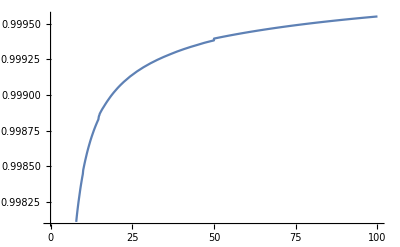

```mathematica
Fd[y_]:=Which[y<4,Pl21[y],4≤y≤16,Pl23[y],16≤y≤50,Pl22[y],y>50,1-λ[y,50]^2];
Plot[Fd[y],{y,0,100}]
```

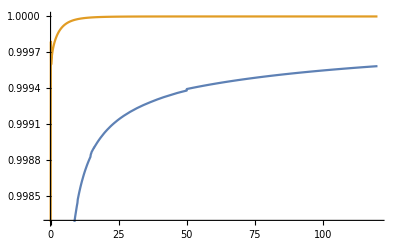

```mathematica
Fd2[y_]:=If[y<99,Pl24[y],1];
Plot[{Fd[y],Fd2[y]},{y,0,120}]
```

```mathematica
1->12
```

```mathematica
ξ[x_,y_,z_]:=(y-x+2*x1*√(z+x))/(2*x1*√y);M1[x_,y_,z_,β_]:=((2*π)/(α*β))^2*(√Abs[1-ξ[x,y,z]^2]*√(y*z)*(y-x-(α*β* λ[y,β] x)/(2(1-x-λ[y,β]^2))Exp[(-2y)/β])^2)/(x*√(x+z)((x1-√(x+z))^2-z))*UnitStep[1-ξ[x,y,z]]*UnitStep[y-x];
In1[x_,y_,z_,β_]:=M1[x,y,z,β]*(1+(α*β)/(2*π)*dH[x,y,β])^-1;
```

```mathematica
W50W1={};x1=.;
For[x1=0, x1≤ 2.75,W50W1=Append[W50W1,{x1,NIntegrate[In1[Fd[y],y,z,50],{y,0,∞},{z,0,∞},Method  -> QuasiMonteCarlo, MaxPoints-> 100000,Compiled->False,PrecisionGoal->2]}],x1=x1+0.25]
```

NIntegrate::maxp: The integral failed to converge after 100000 integrand evaluations. NIntegrate obtained -0.0000131945 and 0.0000198641 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000 integrand evaluations. NIntegrate obtained 0.000310195 and 0.00007498 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000 integrand evaluations. NIntegrate obtained 0.0027176 and 0.000383415 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

```mathematica
W50W2={};x1=.;
For[x1=0, x1≤ 2.75,W50W2=Append[W50W2,{x1,NIntegrate[In1[Fd2[y],y,z,50],{y,0,∞},{z,0,∞},Method  -> QuasiMonteCarlo, MaxPoints-> 500000,Compiled->False,PrecisionGoal->2]}],x1=x1+0.25]
```

NIntegrate::maxp: The integral failed to converge after 459496 integrand evaluations. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

```mathematica
W50W1;
```

```mathematica
{{0.25,-0.000013194480950147668},{0.5,0.00031019501993460527},{0.75,0.002717604576925877},{1.,0.02367018706977363},{1.25,0.19578871067225387},{1.5,0.5559503122153263},{1.75,0.9460873538144916},{2.,1.145759239104823},{2.25,1.2325292874917195},{2.5,1.2768727953183623},{2.75,1.2825075270726898},{3.,1.2573453205089582}}
W50W2
```

{{0.25,-0.0000131945},{0.5,0.000310195},{0.75,0.0027176},{1.,0.0236702},{1.25,0.195789},{1.5,0.55595},{1.75,0.946087},{2.,1.14576},{2.25,1.23253},{2.5,1.27687},{2.75,1.28251},{3.,1.25735}}

{{0.25,0.},{0.5,0.},{0.75,0.},{1.,0.},{1.25,0.00918452},{1.5,0.060007},{1.75,0.164051},{2.,0.3114},{2.25,0.484303},{2.5,0.660281},{2.75,0.825145},{3.,0.965169}}

```mathematica
1->22
```

```mathematica
Dom0[x1_,kx_,ky_]:=(x1^2+Fd[kx^2+ky^2]-Fd[x1^2+kx^2+ky^2-2*x1*kx])^2-4x1^2 Fd[kx^2+ky^2];
M122[x1_,x_,x2_,kx_,ky_,β_]:=(π/(α*β))^2*((x1^2-x-x2)^2)/(x*x1*x2*((x1^2+x-x2)^2-4 x1^2 x)^0.5)*(kx*(x1^2+kx^2+ky^2-2*x1*kx-x2-(α*β*x2*λ[x1^2+kx^2+ky^2-2*x1*kx,β])/(2(1-x2-λ[x1^2+kx^2+ky^2-2*x1*kx,β]^2)))+(x1-kx)(kx^2+ky^2-x-(α*β*x*λ[kx^2+ky^2,β])/(2(1-x-λ[kx^2+ky^2,β]^2))))^2*UnitStep[kx^2+ky^2-x];
```

```mathematica
In11[x1_,kx_,ky_,β_]:=If[Re[Dom0[x1,kx,ky]]≥0,M122[x1,Fd[kx^2+ky^2],Fd[x1^2+kx^2+ky^2-2*x1*kx],kx,ky,β]*(1+(α*β)/(2*π)*dH[Fd[kx^2+ky^2],kx^2+ky^2,β])^-1*(1+(α*β)/(2*π)*dH[Fd[x1^2+kx^2+ky^2-2*x1*kx],x1^2+kx^2+ky^2-2*x1*kx,β])^-1,0];WW11={};x1=.;
For[x1=2.4, x1≤ 2.9,WW11=Append[WW11,{x1,NIntegrate[In11[x1,kx,ky,50],{kx,-∞,∞},{ky,-∞,∞},Method  -> QuasiMonteCarlo, MaxPoints-> 500000,Compiled->False,PrecisionGoal->2]}],x1=x1+0.1]
```

NIntegrate::maxp: The integral failed to converge after 459496 integrand evaluations. NIntegrate obtained 0.417816 and 0.0918023 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 459496 integrand evaluations. NIntegrate obtained 1.19004 and 0.469592 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 459496 integrand evaluations. NIntegrate obtained 1.02664 and 0.126754 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

$Aborted

```mathematica
WW11
```

{{1.,0.417816},{1.1,1.19004},{1.2,1.02664},{1.3,1.6483},{1.4,2.44096},{1.5,2.94051},{1.6,3.26526},{1.7,4.0752},{1.8,4.44487},{1.9,4.40901},{2.,4.03684},{2.1,3.21362},{2.2,2.68188},{2.3,2.17839},{2.4,1.80292}}

```mathematica
Dom1[x1_,kx_,ky_]:=(x1^2+Fd[kx^2+ky^2]-Fd2[x1^2+kx^2+ky^2-2*x1*kx])^2-4x1^2 Fd[kx^2+ky^2];In12[x1_,kx_,ky_,β_]:=If[Re[Dom1[x1,kx,ky]]≥0,M122[x1,Fd[kx^2+ky^2],Fd2[x1^2+kx^2+ky^2-2*x1*kx],kx,ky,β]*(1+(α*β)/(2*π)*dH[Fd[kx^2+ky^2],kx^2+ky^2,β])^-1*(1+(α*β)/(2*π)*dH[Fd2[x1^2+kx^2+ky^2-2*x1*kx],x1^2+kx^2+ky^2-2*x1*kx,β])^-1,0];
WW12={};x1=.;
For[x1=2, x1≤ 2.08,WW12=Append[WW12,{x1,NIntegrate[In12[x1,kx,ky,50],{kx,-∞,∞},{ky,-∞,∞},Method  -> QuasiMonteCarlo, MaxPoints-> 100000,Compiled->False,PrecisionGoal->2]}],x1=x1+0.01]
```

NIntegrate::maxp: The integral failed to converge after 100000 integrand evaluations. NIntegrate obtained 0.220375 and 0.0213595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000 integrand evaluations. NIntegrate obtained 0.211873 and 0.0214218 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000 integrand evaluations. NIntegrate obtained 0.206836 and 0.0214838 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

```mathematica
WW12
```

{{2.01,0.220375},{2.02,0.211873},{2.03,0.206836},{2.04,0.203353},{2.05,0.200767},{2.06,0.198767},{2.07,0.197177},{2.08,0.195892},{2.09,0.19484}}